```mathematica
BoegaInGraph[g_,n_]:=IntegerPart[ N[Total[Map[#&,N[Eigenvalues[MatrixPower[AdjacencyMatrix[g],n]]]]]]/(n!)]
```

```mathematica
EdgeWeights2[g_]:=EdgeWeights2[g,EdgeList[g]]
```

```mathematica
EdgeWeights2[g_,edges_,n_]:=Block[{ weights=Association[]},
Table[
With[{h=EdgeDelete[g,e]},
weights[Sort[e]]=BoegaInGraph[h,n]
]
,{e,edges}
];
weights
]
```

```mathematica
PaintGraph2[g_,n_]:=Block[{weights= EdgeWeights2[g,EdgeList[g],n],maxWeight},
maxWeight = Max[Values[weights]];
If[maxWeight==0,maxWeight=1];
Graph[
Table[
Style[UndirectedEdge[e[[1]],e[[2]]],(ColorData["DarkRainbow"][1-weights[e]/maxWeight])],{e,EdgeList[g]}]
, GraphLayout->"PlanarEmbedding",
EdgeLabels->Table[e->weights[e],{e,EdgeList[g]}],
VertexLabels->"Name",
VertexLabelStyle->Darker[Green]]
]
```

```mathematica
TableGraph[g_,n_]:=Block[{weights= EdgeWeights2[g,EdgeList[g],n],maxWeight},
maxWeight = Max[Values[weights]];
If[maxWeight==0,maxWeight=1];
weights[1<->2]
]
```

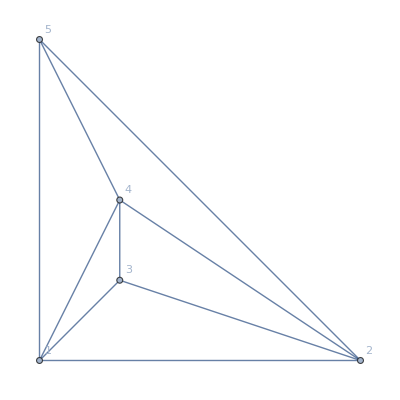
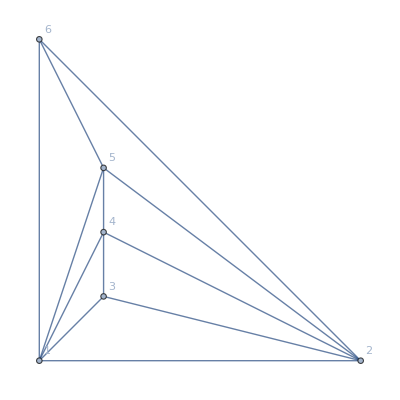
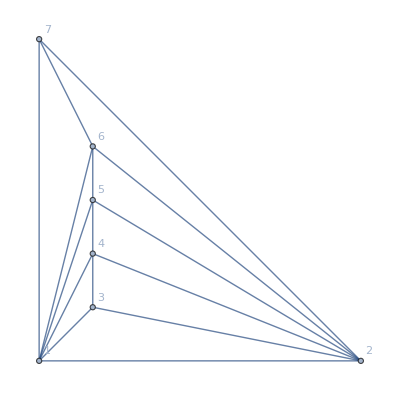
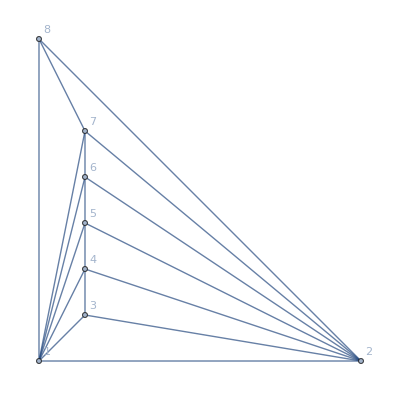
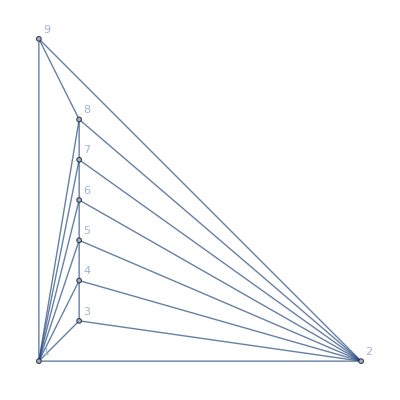
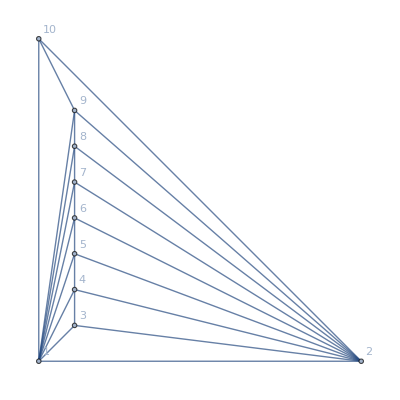
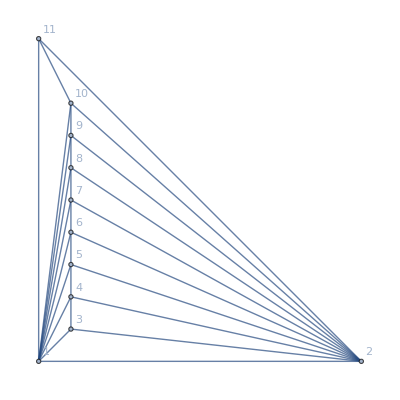
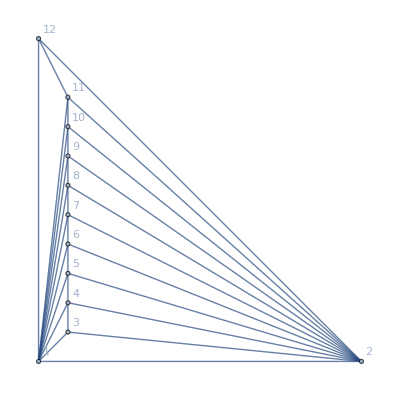
-Graphics-→(k | n | 1<->2 | global
1 | 1 | 0 | 0
1 | 2 | 9 | 8
1 | 3 | 7 | 4
1 | 4 | 7 | 5
1 | 5 | 5 | 2
1 | 6 | 3 | 1
1 | 7 | 1 | 0
1 | 8 | 0 | 0) | -Graphics-→(k | n | 1<->2 | global
2 | 1 | 0 | 0
2 | 2 | 11 | 11
2 | 3 | 10 | 6
2 | 4 | 12 | 9
2 | 5 | 9 | 5
2 | 6 | 6 | 3
2 | 7 | 3 | 1
2 | 8 | 2 | 0) | -Graphics-→(k | n | 1<->2 | global
3 | 1 | 0 | 0
3 | 2 | 15 | 14
3 | 3 | 13 | 8
3 | 4 | 18 | 13
3 | 5 | 15 | 8
3 | 6 | 11 | 6
3 | 7 | 7 | 3
3 | 8 | 4 | 2)
-Graphics-→(k | n | 1<->2 | global
4 | 1 | 0 | 0
4 | 2 | 18 | 17
4 | 3 | 16 | 9
4 | 4 | 24 | 19
4 | 5 | 21 | 12
4 | 6 | 18 | 11
4 | 7 | 12 | 6
4 | 8 | 7 | 3) | -Graphics-→(k | n | 1<->2 | global
5 | 1 | 0 | 0
5 | 2 | 21 | 20
5 | 3 | 19 | 11
5 | 4 | 31 | 25
5 | 5 | 28 | 17
5 | 6 | 25 | 16
5 | 7 | 18 | 9
5 | 8 | 12 | 6) | -Graphics-→(k | n | 1<->2 | global
6 | 1 | 0 | 0
6 | 2 | 24 | 23
6 | 3 | 21 | 14
6 | 4 | 39 | 31
6 | 5 | 37 | 22
6 | 6 | 35 | 23
6 | 7 | 26 | 14
6 | 8 | 18 | 9)
-Graphics-→(k | n | 1<->2 | global
7 | 1 | 0 | 0
7 | 2 | 27 | 25
7 | 3 | 25 | 16
7 | 4 | 47 | 38
7 | 5 | 46 | 28
7 | 6 | 46 | 31
7 | 7 | 36 | 20
7 | 8 | 26 | 14) | -Graphics-→(k | n | 1<->2 | global
8 | 1 | 0 | 0
8 | 2 | 30 | 29
8 | 3 | 28 | 18
8 | 4 | 56 | 46
8 | 5 | 57 | 35
8 | 6 | 60 | 41
8 | 7 | 49 | 27
8 | 8 | 36 | 21) | -Graphics-→(k | n | 1<->2 | global
9 | 1 | 0 | 0
9 | 2 | 33 | 32
9 | 3 | 31 | 20
9 | 4 | 65 | 55
9 | 5 | 68 | 42
9 | 6 | 75 | 52
9 | 7 | 63 | 36
9 | 8 | 49 | 29)
-Graphics-→(k | n | 1<->2 | global
10 | 1 | 0 | 0
10 | 2 | 36 | 35
10 | 3 | 34 | 22
10 | 4 | 76 | 64
10 | 5 | 81 | 50
10 | 6 | 93 | 66
10 | 7 | 80 | 46
10 | 8 | 65 | 39) |  |

```mathematica
Multicolumn[
Table[
With[{g=MinimalGraph[k+3]},
g->MatrixForm[Table[{k,n,BoegaInGraph[g,n],TableGraph[g,n]},{n,1,8}],TableHeadings->{None, {"k","n","1<->2","global"}}]
]
,{k,1,10}]
,Appearance -> "Horizontal"
]
```